```mathematica
f1[μ_?NumericQ]:=NIntegrate[1/(1-μ Cos[α])^(3/2),{α, 0,π}]
f2[μ_?NumericQ]:=NIntegrate[Cos[α]/(1-μ Cos[α])^(3/2),{α, 0,π}]
ξ[x_,z_]:= N[√(x^2+z^2)]
θ[x_,z_]:=N[ArcTan[x/z]]
μ[ξ_, θ_]:=(2 ξ)/(1+ξ^2)Sin[θ]
Ex[ξ_,θ_]:=(ξ Sin[θ])/((1+ξ^2)^(3/2))f1[μ[ξ,θ]]-1/((1+ξ^2)^(3/2))f2[μ[ξ,θ]]
Ez[ξ_,θ_]:=(ξ Cos[θ])/((1+ξ^2)^(3/2))f1[μ[ξ,θ]]
```

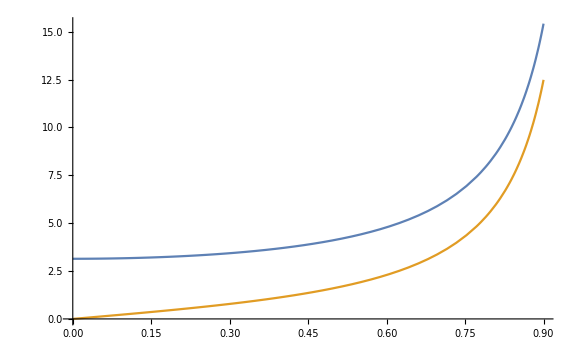

f1f2.png

```mathematica
f1f2 = Plot[{f1[μ],f2[μ]},{μ,0,.9},ImageSize->Large]
Export["f1f2.png",f1f2]
```

```mathematica
fieldxz = VectorPlot[{z/Abs[z] Ex[ξ[x,z],θ[x, z]], z/Abs[z] Ez[ξ[x,z],θ[x, z]]},{x,-2,2},{z,-2,2}, VectorPoints-> 41,VectorColorFunction->"Rainbow",ImageSize->600, VectorAspectRatio->1/4,Prolog->{GrayLevel[.15],Rectangle[Scaled[{-2,-2}],Scaled[{2,2}]]}]
Export["fieldxz.png",fieldxz]
```

-Graphics-

fieldxz.png

```mathematica
fieldxy=VectorPlot[{y/Abs[y] Sin[ArcTan[x/y]]Ex[ξ[√(x^2+y^2),.1],θ[√(x^2+y^2), .1]], y/Abs[y] Cos[ArcTan[x/y]]Ex[ξ[√(x^2+y^2),.1],θ[√(x^2+y^2), .1]]},{x,-2,2},{y,-2,2}, VectorPoints-> 41,VectorColorFunction->"Rainbow",ImageSize->600, VectorAspectRatio->1/4,Prolog->{GrayLevel[.15],Rectangle[Scaled[{-2,-2}],Scaled[{2,2}]]}]
Export["fieldxy.png",fieldxy]
```

-Graphics-

```mathematica
R=1;
r = .05;
L =2;
ringpic = Show[{
VectorPlot3D[{z/Abs[z] x/(√(x^2+y^2))Ex[ξ[√(x^2+y^2),z],θ[√(x^2+y^2), z]],z/Abs[z] y/(√(x^2+y^2))Ex[ξ[√(x^2+y^2),z],θ[√(x^2+y^2), z]],z/Abs[z] Ez[ξ[√(x^2+y^2),z],θ[√(x^2+y^2), z]]},{x,-L,L},{y,-L,L},{z,-L,L},VectorPoints->15,VectorAspectRatio-> 1/5,VectorColorFunction->"Rainbow",ImageSize->600, SphericalRegion->True,VectorStyle->{Opacity[0.9]}], ParametricPlot3D[{(R + r Cos[θ])Cos[ϕ],(R + r Cos[θ])Sin[ϕ], r Sin[θ]}, {θ,0,2π},{ϕ, 0, 2π},Mesh->None],Graphics3D[{InfinitePlane[{{-L,-L,-L},{L,-L,-L},{-L,L,-L}}],InfinitePlane[{{-L,-L,-L},{-L,-L,L},{-L,L,-L}}],InfinitePlane[{{-L,-L,-L},{-L,-L,L},{L,-L,-L}}]},PlotRange->{{-L,L},{-L,L},{-L,L}}]
},ViewPoint->{2Cos[π/5],2Sin[π/5],.6},PlotRange->{{-L,L},{-L,L},{-L,L}},Lighting->{{"Ambient",GrayLevel[.15]}}]
Export["ringpic.png",ringpic]
```

-Graphics3D-

ringpic.png